```mathematica
titles={"He","C","N","O"};
data=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational\ material\ physics /Cluster\ data/P1/noSpin/evals``.tsv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]&/@titles
```

{{{-15.6721,-0.4246,4.2884,4.2884,4.2884},{-15.7259,-0.2158,2.3469,2.3469,2.3469},{-15.7506,-0.1288,1.5249,1.5249,1.5249},{-15.7615,-0.0826,1.0814,1.0814,1.0815}},{{-12.8083,-4.2132,-4.2132,-4.2132,-0.3506,4.1716},{-13.431,-4.9476,-4.9476,-4.9476,-0.6195,2.1395},{-13.617,-5.1392,-5.1392,-5.1392,-0.4641,1.3888},{-13.6864,-5.209,-5.209,-5.209,-0.347,0.9225}},{{-17.7274,-6.1805,-6.1805,-6.1805,-0.6036,4.4319},{-18.329,-6.8165,-6.8165,-6.8165,-0.6101,2.3514},{-18.4722,-6.9608,-6.9608,-6.9608,-0.4227,1.4316},{-18.5317,-7.0211,-7.0211,-7.0211,-0.319,0.8663}},{{-23.2587,-8.308,-8.308,-8.308,-0.7542,4.6154,4.6154},{-23.7661,-8.8249,-8.8249,-8.8249,-0.5773,2.4445,2.4445},{-23.8805,-8.94,-8.94,-8.94,-0.4106,1.4277,1.4611},{-23.9257,-8.9874,-8.9874,-8.9874,-0.3204,0.8022,0.9958}}}

```mathematica
First@data
```

{{-15.6721,-0.4246,4.2884,4.2884,4.2884},{-15.7259,-0.2158,2.3469,2.3469,2.3469},{-15.7506,-0.1288,1.5249,1.5249,1.5249},{-15.7615,-0.0826,1.0814,1.0814,1.0815}}

```mathematica
dataOccs=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational\ material\ physics /Cluster\ data/P1/noSpin/occs``.tsv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]&/@titles;
```

```mathematica
dataOccs
```

{{{2.,0.,0.,0.,0.},{2.,0.,0.,0.,0.},{2.,0.,0.,0.,0.},{2.,0.,0.,0.,0.}},{{2.,0.66667,0.66667,0.66667,0.,0.},{2.,0.66667,0.66667,0.66667,0.,0.},{2.,0.66667,0.66667,0.66666,0.,0.},{2.,0.66667,0.66667,0.66667,0.,0.}},{{2.,1.,1.,1.,0.,0.},{2.,1.,1.,1.,0.,0.},{2.,1.,1.,1.,0.,0.},{2.,1.,1.,1.,0.,0.}},{{2.,1.33333,1.33333,1.33333,0.,0.,0.},{2.,1.33333,1.33333,1.33333,0.,0.,0.},{2.,1.33333,1.33333,1.33333,0.,0.,0.},{2.,1.33333,1.33333,1.33333,0.,0.,0.}}}

```mathematica
TableForm/@Transpose/@data;
```

```mathematica
af=Table[Transpose[{{5,7,9,11},#}]&/@Transpose[f],{f,data}];
```

```mathematica
t=StringForm["`` Å",#]&/@{5,7,9,11}//Evaluate;
plts=Column[{Row[{Grid[Transpose[#4],Frame->All],Grid[Transpose[Rationalize[#3,0.001]],Frame->All]},Spacer[5]],Spacer[1],Row[{Spacer[0],Magnify[Plot[Interpolation[#,Method->"Spline"][x]&/@#1//Evaluate,{x,5,11},PlotLabels->(StringForm["``",#]&/@Range[1,Length[#1]]),Epilog->{Point[#]&/@#1},AxesLabel->{"a (Å)","E (eV)" },PlotRange->{Full,Automatic},ImageSize->Medium],1.1]}]}]&@@@Transpose[{af,titles,dataOccs,data}]
```

{-15.6721 | -15.7259 | -15.7506 | -15.7615
-0.4246 | -0.2158 | -0.1288 | -0.0826
4.2884 | 2.3469 | 1.5249 | 1.0814
4.2884 | 2.3469 | 1.5249 | 1.0814
4.2884 | 2.3469 | 1.5249 | 1.08152 | 2 | 2 | 2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

-Graphics-,-12.8083 | -13.431 | -13.617 | -13.6864
-4.2132 | -4.9476 | -5.1392 | -5.209
-4.2132 | -4.9476 | -5.1392 | -5.209
-4.2132 | -4.9476 | -5.1392 | -5.209
-0.3506 | -0.6195 | -0.4641 | -0.347
4.1716 | 2.1395 | 1.3888 | 0.92252 | 2 | 2 | 2
2/3 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0

-Graphics-,-17.7274 | -18.329 | -18.4722 | -18.5317
-6.1805 | -6.8165 | -6.9608 | -7.0211
-6.1805 | -6.8165 | -6.9608 | -7.0211
-6.1805 | -6.8165 | -6.9608 | -7.0211
-0.6036 | -0.6101 | -0.4227 | -0.319
4.4319 | 2.3514 | 1.4316 | 0.86632 | 2 | 2 | 2
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0

-Graphics-,-23.2587 | -23.7661 | -23.8805 | -23.9257
-8.308 | -8.8249 | -8.94 | -8.9874
-8.308 | -8.8249 | -8.94 | -8.9874
-8.308 | -8.8249 | -8.94 | -8.9874
-0.7542 | -0.5773 | -0.4106 | -0.3204
4.6154 | 2.4445 | 1.4277 | 0.8022
4.6154 | 2.4445 | 1.4611 | 0.99582 | 2 | 2 | 2
4/3 | 4/3 | 4/3 | 4/3
4/3 | 4/3 | 4/3 | 4/3
4/3 | 4/3 | 4/3 | 4/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

-Graphics-}

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/datsevals``.pdf",#1],#2]&@@@Transpose[{titles,plts}];
```

```mathematica
plts2=Plot[Interpolation[#,Method->"Spline"][x]&/@#1//Evaluate,{x,5,11},PlotLabels->(StringForm["``",#]&/@Range[1,Length[#1]]),Epilog->{Point[#]&/@#1},AxesLabel->{"a (Å)","E (eV)" },PlotRange->{Full,Automatic},ImageSize->Medium,PlotLabel->#2]&@@@Transpose[{af,titles,dataOccs,data}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/datsevals``.pdf",#1],#2]&@@@Transpose[{titles,plts2}];
```

```mathematica
dataspin=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational\ material\ physics /Cluster\ data/P1/spin/spinEvals``.tsv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]&/@titles
```

{{{-15.6552,-0.0908,1.559,1.559,1.559,1.7958},{-15.8416,-0.0691,1.5783,1.5783,1.5783,1.7247}},{{-14.5155,-5.9544,-5.9544,-5.9544,-0.5581,1.2732,1.3922},{-11.7524,-3.4672,-3.4672,-3.4672,-0.0937,1.7434,1.7434}},{{-19.7799,-8.1788,-8.1788,-8.1788,-0.4957,1.3397,1.3441},{-15.2094,-4.0253,-4.0253,-4.0253,-0.0439,1.8589,1.859}},{{-25.1382,-10.1315,-10.1315,-10.1315,-0.3726,1.3186,1.5027,1.5027},{-21.89,-7.1036,-7.1036,-7.1036,-0.3126,1.564,1.564,1.5779}}}

```mathematica
dataSpinOccs=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational\ material\ physics /Cluster\ data/P1/spin/spinOccs``.tsv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]&/@titles
```

{{{0.98146,0.,0.,0.,0.,0.},{1.01854,0.,0.,0.,0.,0.}},{{1.,0.66667,0.66667,0.66667,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.}},{{1.,1.,1.,1.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.}},{{1.,1.,1.,1.,0.,0.,0.,0.},{1.,0.33333,0.33333,0.33333,0.,0.,0.,0.}}}

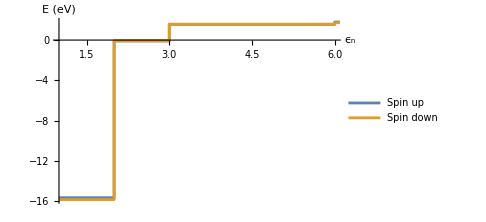
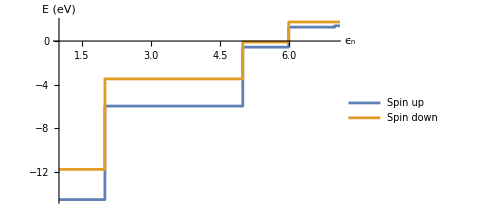
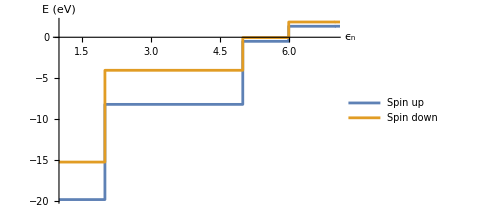
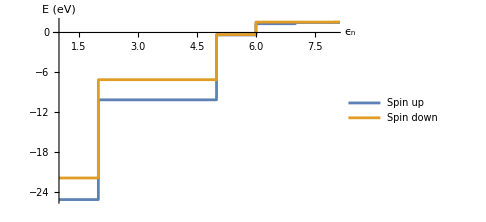
{-15.6552 | -15.8416
-0.0908 | -0.0691
1.559 | 1.5783
1.559 | 1.5783
1.559 | 1.5783
1.7958 | 1.724753/54 | 55/54
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0

-Graphics-,-14.5155 | -11.7524
-5.9544 | -3.4672
-5.9544 | -3.4672
-5.9544 | -3.4672
-0.5581 | -0.0937
1.2732 | 1.7434
1.3922 | 1.74341 | 1
2/3 | 0
2/3 | 0
2/3 | 0
0 | 0
0 | 0
0 | 0

-Graphics-,-19.7799 | -15.2094
-8.1788 | -4.0253
-8.1788 | -4.0253
-8.1788 | -4.0253
-0.4957 | -0.0439
1.3397 | 1.8589
1.3441 | 1.8591 | 1
1 | 0
1 | 0
1 | 0
0 | 0
0 | 0
0 | 0

-Graphics-,-25.1382 | -21.89
-10.1315 | -7.1036
-10.1315 | -7.1036
-10.1315 | -7.1036
-0.3726 | -0.3126
1.3186 | 1.564
1.5027 | 1.564
1.5027 | 1.57791 | 1
1 | 1/3
1 | 1/3
1 | 1/3
0 | 0
0 | 0
0 | 0
0 | 0

-Graphics-}

```mathematica
pltsSpin=Column[{Row[{Spacer[65],Grid[Transpose[#1],Frame->All],Spacer[30],Grid[Rationalize[Transpose[#2],10^-4],Frame->All]}],Spacer[1],Row[{Magnify[ListStepPlot[#1,PlotLegends->{"Spin up","Spin down"},PlotRange->{{1,Full},Full},AxesLabel->{"ϵ_n","E (eV)"},ImageSize->Medium],1.1]}]}]&@@@Transpose[{dataspin,dataSpinOccs}]
```

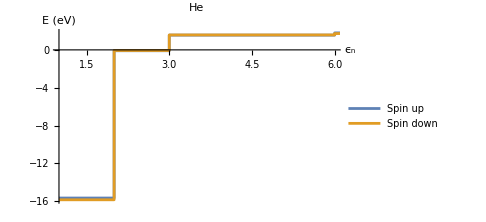
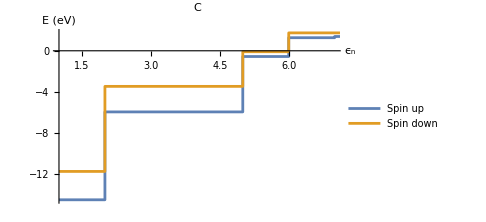
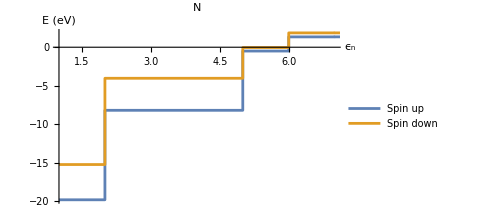
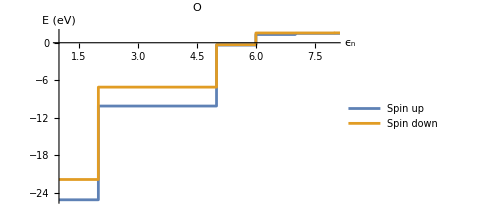

```mathematica
pltsSpin2=ListStepPlot[#1,PlotLegends->{"Spin up","Spin down"},PlotRange->{{1,Full},Full},AxesLabel->{"ϵ_n","E (eV)"},ImageSize->Medium,PlotLabel->#2]&@@@Transpose[{dataspin,titles,dataSpinOccs}]
```

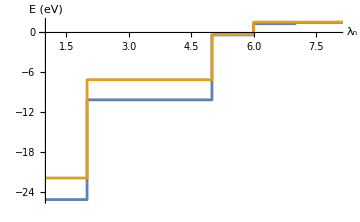
```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/spindatsevalsnoSpin.pdf",-Graphics-]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/spindatsevalsnoSpin.pdf

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/spindatsevals``.pdf",#1],#2]&@@@Transpose[{titles,pltsSpin2}]
```

{/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/spindatsevalsHe.pdf,/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/spindatsevalsC.pdf,/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/spindatsevalsN.pdf,/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/spindatsevalsO.pdf}

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/datsOccs.pdf"],pltsSpin]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/datsOccs.pdf

```mathematica
Transpose[dataspin]
```

{{{-15.6552,-0.0908,1.559,1.559,1.559,1.7958},{-14.5155,-5.9544,-5.9544,-5.9544,-0.5581,1.2732,1.3922},{-19.7799,-8.1788,-8.1788,-8.1788,-0.4957,1.3397,1.3441},{-25.1382,-10.1315,-10.1315,-10.1315,-0.3726,1.3186,1.5027,1.5027}},{{-15.8416,-0.0691,1.5783,1.5783,1.5783,1.7247},{-11.7524,-3.4672,-3.4672,-3.4672,-0.0937,1.7434,1.7434},{-15.2094,-4.0253,-4.0253,-4.0253,-0.0439,1.8589,1.859},{-21.89,-7.1036,-7.1036,-7.1036,-0.3126,1.564,1.564,1.5779}}}

```mathematica
{Rationalize[Transpose[dataSpinOccs],0.001]}
```

{{{{51/52,0,0,0,0,0},{1,2/3,2/3,2/3,0,0,0},{1,1,1,1,0,0,0},{1,1,1,1,0,0,0,0}},{{54/53,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{1,1/3,1/3,1/3,0,0,0,0}}}}

```mathematica
dataspinredO=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational\ material\ physics /Cluster\ data/P1/spin/spinEvalsRedO.tsv"],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"];
```

```mathematica
dataSpinOccsRedO=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational\ material\ physics /Cluster\ data/P1/spin/spinOccsRedO.tsv"],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]
```

{{1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,0.,0.,0.,0.,0.,0.}}

```mathematica
pltsSpinRedO=Column[{Row[{Spacer[65],Grid[Transpose[dataspinredO],Frame->All],Spacer[30],Grid[Rationalize[Transpose[dataSpinOccsRedO],10^-4],Frame->All]}],Spacer[1],Row[{Magnify[ListStepPlot[dataspinredO,PlotLabels->{"Spin up","Spin down"},AxesLabel->{"ϵ_n","E (eV)"},PlotRange->{{1,Full},Full},ImageSize->Medium],1.1]}]}]
```

-25.1379 | -21.4729
-10.8147 | -7.4589
-10.8138 | -6.3531
-8.7139 | -6.3516
-0.4705 | -0.2772
1.0801 | 1.2303
1.1092 | 1.3117
1.4435 | 1.51521 | 1
1 | 1
1 | 0
1 | 0
0 | 0
0 | 0
0 | 0
0 | 0

-Graphics-

```mathematica
Last@data
Last@dataOccs
```

{{-23.2587,-8.308,-8.308,-8.308,-0.7542,4.6154,4.6154},{-23.7661,-8.8249,-8.8249,-8.8249,-0.5773,2.4445,2.4445},{-23.8805,-8.94,-8.94,-8.94,-0.4106,1.4277,1.4611},{-23.9257,-8.9874,-8.9874,-8.9874,-0.3204,0.8022,0.9958}}

{{2.,1.33333,1.33333,1.33333,0.,0.,0.},{2.,1.33333,1.33333,1.33333,0.,0.,0.},{2.,1.33333,1.33333,1.33333,0.,0.,0.},{2.,1.33333,1.33333,1.33333,0.,0.,0.}}

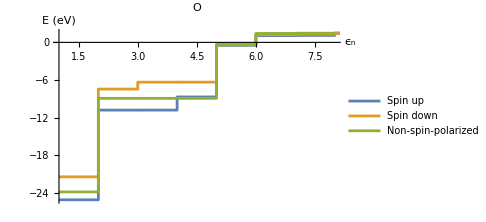

```mathematica
pltsSpinRedO2=ListStepPlot[Join[dataspinredO,{(Last@data)[[3]]}],PlotLegends->{"Spin up","Spin down","Non-spin-polarized"},AxesLabel->{"ϵ_n","E (eV)"},PlotRange->{{1,Full},Full},ImageSize->Medium,PlotLabel->"O"]
```

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/datsOccsRedO.pdf"],pltsSpinRedO2]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/datsOccsRedO.pdf

```mathematica
imgs=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P1/out/PARCHG_p``.png",#],ImageSize->Full]&/@{"x","y","z"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/orbsP.png",Row[imgs]]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/1/orbsP.png